# The P&M Social Network

## March 2017

## Data import

```mathematica
dataset=SemanticImport["/Users/cwoodard/GitHub/PaM2017/graphs/pm-teams-mar2017.csv"]
```

Dataset[<>]

## Graph construction

First, let’s group the data by teams for each experiment:

```mathematica
exp0=dataset[GroupBy["Exp0"]]
```

Dataset[<>]

```mathematica
exp1=dataset[GroupBy["Exp1"]];
exp2=dataset[GroupBy["Exp2"]];
exp3=dataset[GroupBy["Exp3"]];
```

Now let’s extract the node IDs:

```mathematica
exp0Nodes=Normal@Values[exp0[All,All,"Node"]]
```

{{1,29,52,63},{2,30,32,38},{3,23,34,48},{4,39,54,83},{5,6,77,82},{7,10,18,71},{8,25,27,62},{9,26,42,46},{11,24,59,78},{12,33,36,51},{13,40,47,69},{14,37,74,80},{15,45,66,79},{16,35,64,72},{17,28,44},{19,43,49,57},{20,41,53,81},{21,50,65,76},{22,55,58,73},{31,56,60,75},{61,67,68,70}}

```mathematica
exp1Nodes=Normal@Values[exp1[All,All,"Node"]];
exp2Nodes=Normal@Values[exp2[All,All,"Node"]];
exp3Nodes=Normal@Values[exp3[All,All,"Node"]];
```

Okay, now we need some functions or things are going to get really messy:

```mathematica
completeGraphRawPairs[n_]:=Flatten[Table[{i,j+1},{i,1,n-1},{j,i,n-1}],1]
completeGraphMappedPairs[nodes_List]:=Part[nodes,#]&/@completeGraphRawPairs[Length[nodes]]
completeGraphEdges[nodes_List]:=UndirectedEdge[#[[1]],#[[2]]]&/@completeGraphMappedPairs[nodes]
```

```mathematica
g0edges=Style[#,ColorData[1,0]]&/@Flatten[completeGraphEdges/@exp0Nodes]
```

{1<->29,1<->52,1<->63,29<->52,29<->63,52<->63,2<->30,2<->32,2<->38,30<->32,30<->38,32<->38,3<->23,3<->34,3<->48,23<->34,23<->48,34<->48,4<->39,4<->54,4<->83,39<->54,39<->83,54<->83,5<->6,5<->77,5<->82,6<->77,6<->82,77<->82,7<->10,7<->18,7<->71,10<->18,10<->71,18<->71,8<->25,8<->27,8<->62,25<->27,25<->62,27<->62,9<->26,9<->42,9<->46,26<->42,26<->46,42<->46,11<->24,11<->59,11<->78,24<->59,24<->78,59<->78,12<->33,12<->36,12<->51,33<->36,33<->51,36<->51,13<->40,13<->47,13<->69,40<->47,40<->69,47<->69,14<->37,14<->74,14<->80,37<->74,37<->80,74<->80,15<->45,15<->66,15<->79,45<->66,45<->79,66<->79,16<->35,16<->64,16<->72,35<->64,35<->72,64<->72,17<->28,17<->44,28<->44,19<->43,19<->49,19<->57,43<->49,43<->57,49<->57,20<->41,20<->53,20<->81,41<->53,41<->81,53<->81,21<->50,21<->65,21<->76,50<->65,50<->76,65<->76,22<->55,22<->58,22<->73,55<->58,55<->73,58<->73,31<->56,31<->60,31<->75,56<->60,56<->75,60<->75,61<->67,61<->68,61<->70,67<->68,67<->70,68<->70}

```mathematica
g1edges=Style[#,ColorData[1,1]]&/@Flatten[completeGraphEdges/@exp1Nodes];
g2edges=Style[#,ColorData[1,2]]&/@Flatten[completeGraphEdges/@exp2Nodes];
g3edges=Style[#,ColorData[1,3]]&/@Flatten[completeGraphEdges/@exp3Nodes];
```

Voilà! Our first graph:

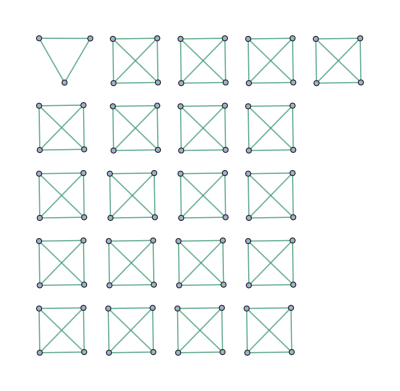

```mathematica
graph0=Graph[g0edges]
```

```mathematica
graph1=Graph[g1edges];
graph2=Graph[g2edges];
graph3=Graph[g3edges];
```

## Graph manipulation

Now let’s put them together …

```mathematica
g01edges=Join[g0edges,g1edges]
```

{1<->29,1<->52,1<->63,29<->52,29<->63,52<->63,2<->30,2<->32,2<->38,30<->32,30<->38,32<->38,3<->23,3<->34,3<->48,23<->34,23<->48,34<->48,4<->39,4<->54,4<->83,39<->54,39<->83,54<->83,5<->6,5<->77,5<->82,6<->77,6<->82,77<->82,7<->10,7<->18,7<->71,10<->18,10<->71,18<->71,8<->25,8<->27,8<->62,25<->27,25<->62,27<->62,9<->26,9<->42,9<->46,26<->42,26<->46,42<->46,11<->24,11<->59,11<->78,24<->59,24<->78,59<->78,12<->33,12<->36,12<->51,33<->36,33<->51,36<->51,13<->40,13<->47,13<->69,40<->47,40<->69,47<->69,14<->37,14<->74,14<->80,37<->74,37<->80,74<->80,15<->45,15<->66,15<->79,45<->66,45<->79,66<->79,16<->35,16<->64,16<->72,35<->64,35<->72,64<->72,17<->28,17<->44,28<->44,19<->43,19<->49,19<->57,43<->49,43<->57,49<->57,20<->41,20<->53,20<->81,41<->53,41<->81,53<->81,21<->50,21<->65,21<->76,50<->65,50<->76,65<->76,22<->55,22<->58,22<->73,55<->58,55<->73,58<->73,31<->56,31<->60,31<->75,56<->60,56<->75,60<->75,61<->67,61<->68,61<->70,67<->68,67<->70,68<->70,1<->19,1<->29,1<->37,19<->29,19<->37,29<->37,2<->22,2<->24,2<->48,22<->24,22<->48,24<->48,3<->7,3<->18,3<->83,7<->18,7<->83,18<->83,4<->11,4<->47,4<->66,11<->47,11<->66,47<->66,5<->8,5<->67,5<->78,8<->67,8<->78,67<->78,6<->36,6<->61,6<->79,36<->61,36<->79,61<->79,9<->15,9<->26,9<->82,15<->26,15<->82,26<->82,10<->39,10<->44,10<->62,39<->44,39<->62,44<->62,12<->41,12<->42,12<->72,41<->42,41<->72,42<->72,13<->21,13<->23,13<->60,21<->23,21<->60,23<->60,14<->31,14<->35,14<->53,31<->35,31<->53,35<->53,16<->40,16<->50,16<->58,40<->50,40<->58,50<->58,17<->27,17<->30,17<->38,27<->30,27<->38,30<->38,20<->25,20<->49,20<->57,25<->49,25<->57,49<->57,28<->69,28<->81,69<->81,32<->71,32<->77,32<->80,71<->77,71<->80,77<->80,33<->45,33<->59,33<->75,45<->59,45<->75,59<->75,34<->43,34<->54,34<->70,43<->54,43<->70,54<->70,46<->64,46<->65,46<->68,64<->65,64<->68,65<->68,51<->52,51<->55,51<->74,52<->55,52<->74,55<->74,56<->63,56<->73,56<->76,63<->73,63<->76,73<->76}

```mathematica
g012edges=Join[g01edges,g2edges];
g0123edges=Join[g012edges,g3edges];
```

And plot the graphs:

```mathematica
graph0
```

-Graphics-

```mathematica
graph01=Graph[g01edges]
```

-Graphics-

```mathematica
graph012=Graph[g012edges]
```

-Graphics-

```mathematica
graph0123=Graph[g0123edges]
```

-Graphics-

And here’s an animation, just for fun:

```mathematica
gl0=Labeled[graph0,"After Experiment 0"];
gl01=Labeled[graph01,"After Experiment 1"];
gl012=Labeled[graph012,"After Experiment 2"];
gl0123=Labeled[graph0123,"After Experiment 3"];
```

```mathematica
graphSequence={graph0,graph01,graph012,graph0123};
labeledGraphSequence={gl0,gl01,gl012,gl0123};
```

```mathematica
anim=Animate[Part[labeledGraphSequence,i],{i,1,4,1},SaveDefinitions->True,AnimationRunning->False]
```

Which we can deploy to the cloud …

```mathematica
(* CloudDeploy[anim,Permissions->"Public"] *)
```

## Graph analysis

And here is some rudimentary graph analysis:

```mathematica
ConnectedGraphQ[graph0]
```

False

```mathematica
ConnectedGraphQ[graph01]
```

True

```mathematica
VertexCount/@graphSequence
```

{83,83,83,83}

```mathematica
meanGraphDistances=MeanGraphDistance/@graphSequence//N
```

{∞,3.12195,2.39935,2.11284}

```mathematica
Max@GraphDistanceMatrix[#]&/@graphSequence
```

{∞,6,4,3}

So — successive randomizing makes the graph smaller … no surprise there!

### Now your turn …

I’m out of time, but there’s lots of other fun stuff to do here:

• Are there any especially interesting nodes, from a network point of view? (We wouldn’t expect any “Kevin Bacons” in a random graph, but someone has to be the most central node …)

• Can you compute statistics on people staying in the same studio between experiments? (How many people have been in the same studio n times in a row? Has everyone now been in the same studio with every other member of the Class of 2020 at least once?)

• What happens if you plot relationships between teams instead of individuals? (Could you lay out the graph from left to right, using directed edges to show people moving from one team to the next? Can you track the progression of project topics through the three main experiments?)

Enjoy!